```mathematica
ClearAll["Global`*"];
Δ1=0.5;
Δ2=1;
ϵ=0.75;
λ=3.0;
δ=0;
λp=λ (1-δ); (*+ ->-*)
λm=λ (1+δ); (*- ->+*)
δm=-Δ1/ϵ;
left=(Δ2-ϵ)/(Δ2-Δ1)+10^-6;
right=1-10^-6;
Πm[x_]=x^(-2 λ (Δ2+δ ϵ)/(Δ2^2-ϵ^2)-1) (1-x)^(2 λ (Δ1+δ ϵ)/(Δ1^2-ϵ^2)-1) Abs[(Δ1-Δ2) x+Δ2+ϵ]^(λ (1-δ) (Δ1-Δ2)/(Δ1+ϵ)/(Δ2+ϵ)) Abs[(Δ1-Δ2) x+Δ2-ϵ]^(λ (1+δ) (Δ1-Δ2)/(Δ1-ϵ)/(Δ2-ϵ)-1);Πp[x_]=x^(-2 λ (Δ2+δ ϵ)/(Δ2^2-ϵ^2)-1) (1-x)^(2 λ (Δ1+δ ϵ)/(Δ1^2-ϵ^2)-1) Abs[(Δ1-Δ2) x+Δ2+ϵ]^(λ (1-δ) (Δ1-Δ2)/(Δ1+ϵ)/(Δ2+ϵ)-1) Abs[(Δ1-Δ2) x+Δ2-ϵ]^(λ (1+δ) (Δ1-Δ2)/(Δ1-ϵ)/(Δ2-ϵ));

Π[x_,λ_, δ_]:=x^(-2 λ (Δ2+δ ϵ)/(Δ2^2-ϵ^2)-1) ( 1-x)^(2 λ (Δ1+δ ϵ)/(Δ1^2-ϵ^2)-1) Abs[(Δ1-Δ2) x+Δ2+ϵ]^(λ (1-δ) (Δ1-Δ2)/(Δ1+ϵ)/(Δ2+ϵ)-1) Abs[(Δ1-Δ2) x+Δ2-ϵ]^(λ (1+δ) (Δ1-Δ2)/(Δ1-ϵ)/(Δ2-ϵ)-1); 
P[x_, λ_, δ_] := Π[x,λ,δ]/NIntegrate[Π[t,λ,δ], {t, left, right}];
```

```mathematica
tab =ParallelTable[{x,δ,P[x,λ,δ]}, {x, left, right, 0.01}, {δ, -0.95, δm-0.05, 0.01}];
```

```mathematica
plot = ListPlot3D[Flatten[tab,1], PlotRange->Full,ColorFunction->Function[{x,y,z},ColorData["RedBlueTones"][y]],
AxesLabel->{Style["x", Bold],Style[ "δ", Bold], Style["Π(x)", Bold]}, Ticks->{True,True,True},Axes->{True,True,True}, Boxed->False,AxesEdge->{{-1,-1},{-1,-1},{-1,1}},
BaseStyle->{FontSize->14}]
```

```mathematica
RunSimulationHist[paramsList_,numInvocations_:Integer,xlow_:NumericQ,xhigh_:NumericQ]:=Module[{lines,inputString,output,ys,asd},lines=(StringRiffle[ToString/@Join[#,{numInvocations,N[xlow],N[xhigh]}]," "]&)/@paramsList;
inputString=StringRiffle[Prepend[lines,ToString[Length[paramsList]]],"\n"];
output=RunProcess[{"wsl", "~/projects/kinetic/bin/pdmp_example"},"StandardOutput",inputString];
asd=StringSplit[StringTrim[output]];
ys=Internal`StringToMReal/@asd;
ys];
```

```mathematica
plt1=Show[
ListLinePlot[{
ParallelTable[{x,P[x,λ,-0.95]}, {x, left, right, 0.01}],
ParallelTable[{x,P[x,λ,-0.72]}, {x, left, right, 0.01}]
}, PlotStyle->{{DarkRed, Dashed}, {DarkGreen, Dashed}, {DarkBlue, Dashed}}],
SmoothHistogram[ {
RunSimulationHist[{{ Δ1,Δ2, ϵ,0, -0.95, λ, 0  }}, 20000, 0, 1],
RunSimulationHist[{{ Δ1,Δ2, ϵ, 0,-0.72, λ, 0  }}, 20000, 0, 1]
},  0.005, "PDF", PlotStyle->{Red, Green, Blue}],
PlotRange->{0, 15}, Frame->True, FrameLabel->{"x", "Π(x)"}, BaseStyle->{FontSize->14}, ImageSize->Medium]
plt2=Show[
ListLinePlot[{
ParallelTable[{x,P[x,λ,-0.8]}, {x, left, right, 0.01}]
}, PlotStyle->{{DarkBlue, Dashed}}],
SmoothHistogram[ {
RunSimulationHist[{{ Δ1,Δ2, ϵ,0, -0.8, λ, 0  }}, 20000, 0, 1]
},  0.005, "PDF", PlotStyle->{Blue}],
PlotRange->Full, Frame->True, FrameLabel->{"x", "Π(x)"}, BaseStyle->{FontSize->14}, ImageSize->Medium]

Export["./DominanceBiased1.pdf", plt1]
Export["./DominanceBiased2.pdf", plt2]
```

```mathematica
ClearAll["Global`*"];
Δ1=-1;
Δ2=1;
ϵ=0.8;
λ1=0.1;
λ2=0.4;
λ3=2.5;
left=(Δ2-ϵ)/(Δ2-Δ1)+10^-6;
right=(Δ2+ϵ)/(Δ2-Δ1)-10^-6;
RunSimulationHist[paramsList_,numInvocations_:Integer,xlow_:NumericQ,xhigh_:NumericQ]:=Module[{lines,inputString,output,ys,asd},lines=(StringRiffle[ToString/@Join[#,{numInvocations,N[xlow],N[xhigh]}]," "]&)/@paramsList;
inputString=StringRiffle[Prepend[lines,ToString[Length[paramsList]]],"\n"];
output=RunProcess[{"ssh", "compute2", "~/projects/kinetic/bin/pdmp_example"},"StandardOutput",inputString];
asd=StringSplit[StringTrim[output ]];
ys=Internal`StringToMReal/@asd;
ys];
GetHistogram[Δ1_?NumericQ, Δ2_?NumericQ, ϵ_?NumericQ,λ_?NumericQ, δ_?NumericQ,
 numInvocations_:10000 ? IntegerQ, xLow_:0?NumericQ, xHigh_:1?NumericQ ,
asymmetricNoise:False?BooleanQ, simulationTimeOverride:0?NumericQ]:= RunSimulationHist[{Δ1, Δ2, ϵ, If[asymmetricNoise, 1, 0], δ, λ, simulationTimeOverride },
numInvocations, xLow, xHigh] ; 

Π[x_,λ_, δ_]:=x^(-2 λ (Δ2+δ ϵ)/(Δ2^2-ϵ^2)-1) ( 1-x)^(2 λ (Δ1+δ ϵ)/(Δ1^2-ϵ^2)-1) Abs[(Δ1-Δ2) x+Δ2+ϵ]^(λ (1-δ) (Δ1-Δ2)/(Δ1+ϵ)/(Δ2+ϵ)-1) Abs[(Δ1-Δ2) x+Δ2-ϵ]^(λ (1+δ) (Δ1-Δ2)/(Δ1-ϵ)/(Δ2-ϵ)-1); 

numInvoc = 10000;
(Δ2^2+ϵ*ϵ)/(2Δ2)
(Δ2^2-ϵ*ϵ)/(2Δ2)
C1 = NIntegrate[Π[t,λ1,0], {t, left, right}]
C2 = NIntegrate[Π[t,λ2,0], {t, left, right}]
C3 = NIntegrate[Π[t,λ3,0], {t, left, right}]
tab =Table[{x,Π[x,λ1,0]/C1}, {x, left, right, (right-left)/50}];
tab2 = RunSimulationHist[{{ Δ1,Δ2, ϵ,0, 0,λ1, 0  }}, numInvoc, 0, 1];
tab3 =Table[{x,Π[x,λ2, 0]/C2}, {x, left, right, (right-left)/50}];
tab4 = RunSimulationHist[{{ Δ1,Δ2, ϵ, 0,0,λ2, 0  }}, numInvoc, 0, 1];
tab5 =Table[{x,Π[x,λ3,0]/C3}, {x, left, right, (right-left)/50}];
tab6 = RunSimulationHist[{{ Δ1,Δ2, ϵ, 0,0,λ3, 0  }}, numInvoc, 0, 1];
```

0.82

0.18

27.409

48.3359

963048.

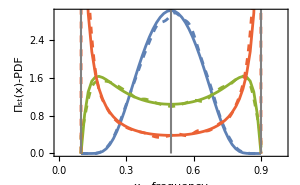

./Documents/Coexistence/CoexistencePlots.svg

```mathematica
plt= Show[
SmoothHistogram[tab6, 0.02, "PDF",  PlotRange->{{left,right},Full},PlotStyle->{ColorData[97,1], Dashed}], 
ListLinePlot[tab5, PlotRange->{{0,1},Full}, PlotStyle->{ColorData[97,1]}],
SmoothHistogram[tab4, 0.02, "PDF",  PlotRange->{{left,right},Full},PlotStyle->{ColorData[97,3], Dashed}], 
ListLinePlot[tab3,  PlotRange->{{0,1},Full},PlotStyle->{ColorData[97,3]}],
SmoothHistogram[tab2, 0.02, "PDF", PlotRange->{{left,right},Full}, PlotStyle->{ColorData[97,4], Dashed}], 
ListLinePlot[tab,  PlotRange->{{0,1},Full},PlotStyle->{ColorData[97,4]}],
ListLinePlot[{{0.5, 0}, {0.5, 10}},  PlotRange->{{0,1},Full},PlotStyle->{Gray, Thickness[0.005]},PlotRange->{{0, 1}, Full}],
ListLinePlot[{{left, 0}, {left, 10}},  PlotRange->{{0,1},Full},PlotStyle->{Gray, Thickness[0.005]},PlotRange->{{0, 1}, Full}],
ListLinePlot[{{right, 0}, {right, 10}}, PlotRange->{{0,1},Full}, PlotStyle->{Gray, Thickness[0.005]},PlotRange->{{0, 1}, Full}],
PlotRange->{{0, 1}, {0,3}}, Frame->True, FrameLabel->{"x - frequency", "Π_st(x)-PDF"}, BaseStyle->{FontSize->14}, ImageSize->300
]
Export["./Documents/Coexistence/CoexistencePlots.svg", plt]
```

```mathematica
Tf=15.0;
numSims = 1000;

getData[Δ1_,Δ2_, ϵ_, λ_] := Block[{left, right, sims, tab,f,g, Simulate2}, 
f[x_]=x*(1-x)*(Δ2+(Δ1-Δ2) x);
       g[x_]=x*(1-x)*ϵ;
Simulate2=ParametricNDSolve[{
y'[t]==f[y[t]]+ξ[t]*g[y[t]],
h'[t]==2*λ67,
WhenEvent[h[t]>=tn[t],{ξ[t]->If[RandomReal[]<=(1-δ)/2,-1,1],
h[t]->0,tn[t]->RandomVariate[ExponentialDistribution[1]]}],
tn[0]== tn0,
y[0]==y0,
h[0]==0,
ξ[0]==ξ0},
{y,h, ξ},{t,0,Tf},
{y0,ξ0,λ67,δ, tn0},(*parameters*)
DiscreteVariables->{ξ,tn}];
left=(Δ2-ϵ)/(Δ2-Δ1)+10^-4;
	right=(Δ2+ϵ)/(Δ2-Δ1)-10^-4;
sims = ParallelTable[
(y[RandomReal[], RandomChoice[{-1, 1}], λ, 0 , RandomVariate[ExponentialDistribution[1]]]) /. Simulate2, 
{numSims}];
tab = Table[
{t, sims[[i]][t]}, 
{t, 0, Tf, Tf/100},
{i, 0, numSims}
];
Transpose[tab]
 ]

data1 = getData[Δ1,Δ2, ϵ, λ1];
data2 = getData[Δ1, Δ2, ϵ, λ2];
data3 = getData[Δ1, Δ2, ϵ, λ3];
```

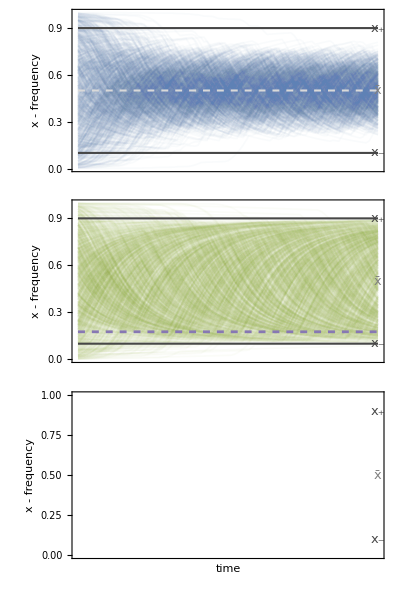

./Documents/Coexistence/CoexistenceTrajectories.svg

```mathematica
sz=300;

labelEpilog[Tf_,left_,right_]:={
Text[Style[Subscript["x","-"],DarkGray,13],{Tf,left},{-2.5,0}],
Text[Style[Subscript["x","+"],DarkGray,13],{Tf,right},{-2.5,0}],
Text[Style[OverBar["x"],Gray,13],{Tf,0.5},{-3.5,0}]};

getPlot[data_,l_]:=Block[{},
Show[
ListLinePlot[data,PlotStyle->Directive[ColorData[97,l],Opacity[0.03],Thickness[0.004]],Frame->True,FrameTicks->{If[l==3,True,False],True},BaseStyle->{FontSize->14},ImageSize->sz],
ListLinePlot[{{{0,left},{Tf,left}},{{0,right},{Tf,right}},{{0,0.5},{Tf,0.5}}},PlotStyle->{Directive[DarkGray,Thickness[0.005]],Directive[DarkGray,Thickness[0.005]],Directive[If[l==1,LightGray,Gray],Dashed,Thickness[0.005]]}],Epilog->labelEpilog[Tf,left,right],ImagePadding->{{Automatic,40},{Automatic,Automatic}},PlotRangeClipping->False,FrameLabel->{
If[l == 4, "time", None], "x - frequency"}
]];

getPlot2[data_,l_]:=Block[{m1,m2},m1=x/. Last[FindMaximum[Π[x,λ2,0],{x,left,0.4}]];
m2=x/. Last[FindMaximum[Π[x,λ2,0],{x,0.6,right}]];
Show[ListLinePlot[data,PlotStyle->Directive[ColorData[97,l],Opacity[0.03],Thickness[0.004]],Frame->True,FrameTicks->{False,True},BaseStyle->{FontSize->14},ImageSize->sz],ListLinePlot[{{{0,left},{Tf,left}},{{0,right},{Tf,right}},{{0,m1},{Tf,m1}},{{0,m2},{Tf,m2}},{{0,0.5},{Tf,0.5}}},PlotStyle->{Directive[DarkGray,Thickness[0.005]],Directive[DarkGray,Thickness[0.005]],Directive[ColorData[97,5],Dashed],Directive[ColorData[97,5],Dashed],Directive[Gray,Dashed,Thickness[0.005]]}],Epilog->labelEpilog[Tf,left,right],ImagePadding->{{Automatic,40},{Automatic,Automatic}},PlotRangeClipping->False,FrameLabel->{None, "x - frequency"}]];

finalplt=Show[GraphicsColumn[{getPlot[data3,1],getPlot2[data2,3],getPlot[data1,4]}, Spacings->Scaled[0.02]]]
Export["./Documents/Coexistence/CoexistenceTrajectories.svg", finalplt]
```

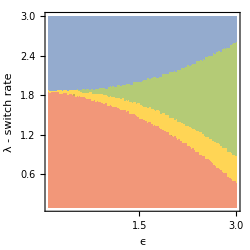

./Documents/Coexistence/CoexistenceExtrema(A=-4,B=3.5).svg

```mathematica
ClearAll["Global`*"];

Π[x_,Δ1_, Δ2_, ϵ_,λ_, δ_]:=x^(-2 λ (Δ2+δ ϵ)/(Δ2^2-ϵ^2)-1) ( 1-x)^(2 λ (Δ1+δ ϵ)/(Δ1^2-ϵ^2)-1) Abs[(Δ1-Δ2) x+Δ2+ϵ]^(λ (1-δ) (Δ1-Δ2)/(Δ1+ϵ)/(Δ2+ϵ)-1) Abs[(Δ1-Δ2) x+Δ2-ϵ]^(λ (1+δ) (Δ1-Δ2)/(Δ1-ϵ)/(Δ2-ϵ)-1); 
(*2. Master Equations*)extrema[x_,α_, β_, ϵ_,λ_]:=(*(-4 x^3 (α-β)^2+β^2-β ϵ+3 x^2 (α-β) (α-3 β+ϵ)+2 β λ-ϵ λ-2 x β (3 β-2 ϵ+λ)+2 x α (2 β-ϵ+λ));*)1/2 (α^2 (3-4 x) x^2-β^2 (-1+x)^2 (-1+4 x)+(-1+2 x) ϵ^2+2 β (-1+x) (2 α x (-1+2 x)-λ)+2 α x λ);
extremaDx[x_,α_,β_,ε_,λ_]:=Evaluate[D[extrema[z,α,β,ε,λ],z]/. z->x];
xm[α_,β_,ϵ_]:=(β-ϵ)/(β-α);
xp[α_,β_,ϵ_]:=(β+ϵ)/(β-α);
(*3. Numerical Root Counter*)
countExtrema[α_?NumericQ,β_?NumericQ,ϵ_?NumericQ,λ_?NumericQ]:=Module[{xmm,xpp,roots,nr},xmm=xm[α,β,ϵ];
xpp=xp[α,β,ϵ];
roots=x/. Quiet@NSolve[extrema[x,α,β,ϵ,λ]==0&&xmm<=x<=xpp,x,Reals];
nr = Length[roots];
If[nr==2,
If[(λ (α-β)/(α+ϵ)/(β+ϵ)-1)>0 , 2, 5], 
If [nr==1,
 If[extremaDx[First[roots],α,β,ϵ,λ]<0, 1, 4], 
nr]]
];

Δ2=4.0;
Δ1=-3.5;
(*4. High-Resolution Parallel Grid Generation*)
gridData=Flatten[ParallelTable[{ϵVal,λVal,countExtrema[Δ1, Δ2, ϵVal,λVal]},{ϵVal,0.1,3.0,0.02},{λVal,0.1,3,0.02}],1];
colorFn = Function[z,Lighter[Switch[Round[z],0,Gray,1,ColorData[97,1],2,ColorData[97, 8], 3,ColorData[97, 3],4, ColorData[97, 4], 5, Darker[ColorData[97, 8]]]]];
(*5. Render Plot with Exact Black/Orange Journal Styling*)
plot1=ListDensityPlot[gridData,InterpolationOrder->0,ColorFunction->colorFn,ColorFunctionScaling->False,
Frame->True,
FrameLabel->{"ϵ","λ - switch rate"},
BaseStyle->{FontSize->14}, ImageSize->250,
ImageSize->Medium]

Export["./Documents/Coexistence/CoexistenceExtrema(A=-4,B=3.5).svg", plot1]
```

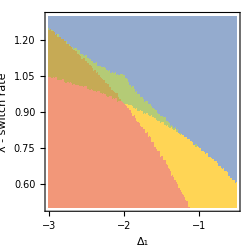

./Documents/Coexistence/CoexistenceExtrema(B=2,E=0.5).svg

```mathematica
Δ2=2;
ϵ=0.5;
(*4. High-Resolution Parallel Grid Generation*)
gridData=Flatten[ParallelTable[{αVal,λVal,countExtrema[αVal, Δ2, ϵ,λVal]},{αVal,-3, -0.51, 0.01},{λVal,0.5, 1.3, 0.01}],1];

(*5. Render Plot with Exact Black/Orange Journal Styling*)
plot2=ListDensityPlot[gridData,InterpolationOrder->0,ColorFunction->colorFn,ColorFunctionScaling->False,
Frame->True,
FrameLabel->{"Δ_1","λ - switch rate"},
BaseStyle->{FontSize->14}, ImageSize->250,
ImageSize->Medium,
FrameTicks->{{Automatic,Automatic},{Charting`ScaledTicks[{Identity,Identity}],None}}]

Export["./Documents/Coexistence/CoexistenceExtrema(B=2,E=0.5).svg", plot2]
```

Power::infy: Infinite expression 1/0.^0.12 encountered.

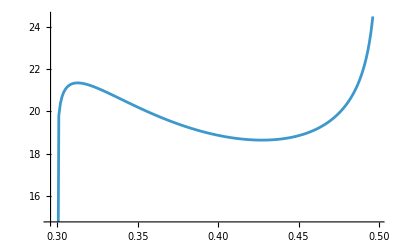

```mathematica
α=-3;
β=2;
ϵ=0.5;
λ=1.1;
ListLinePlot[Table[{x, Π[x,α,β,ϵ,λ, 0]},
 {x, xm[α,β,ϵ], xp[α,β,ϵ], 0.001}]]
```